/Users/eliasberriochoaesnaola

1/2 (1/z+z) Sin[2/(1/z+z)]

Interval[{-∞,∞}]

{Listable}

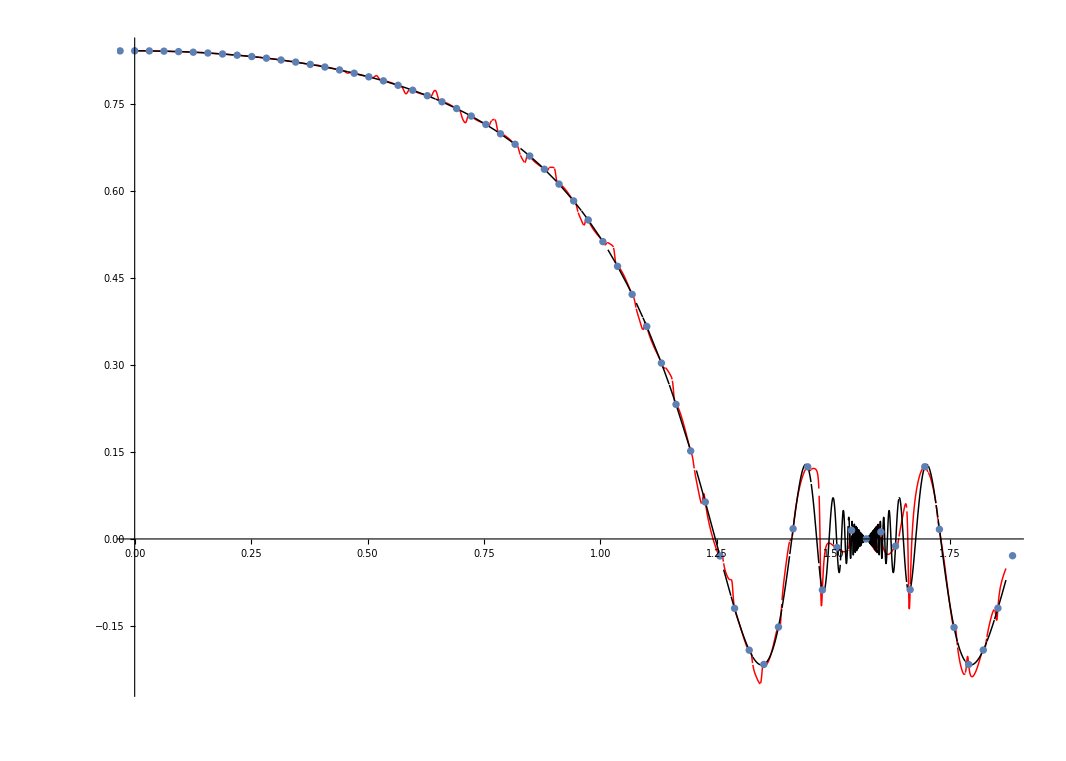

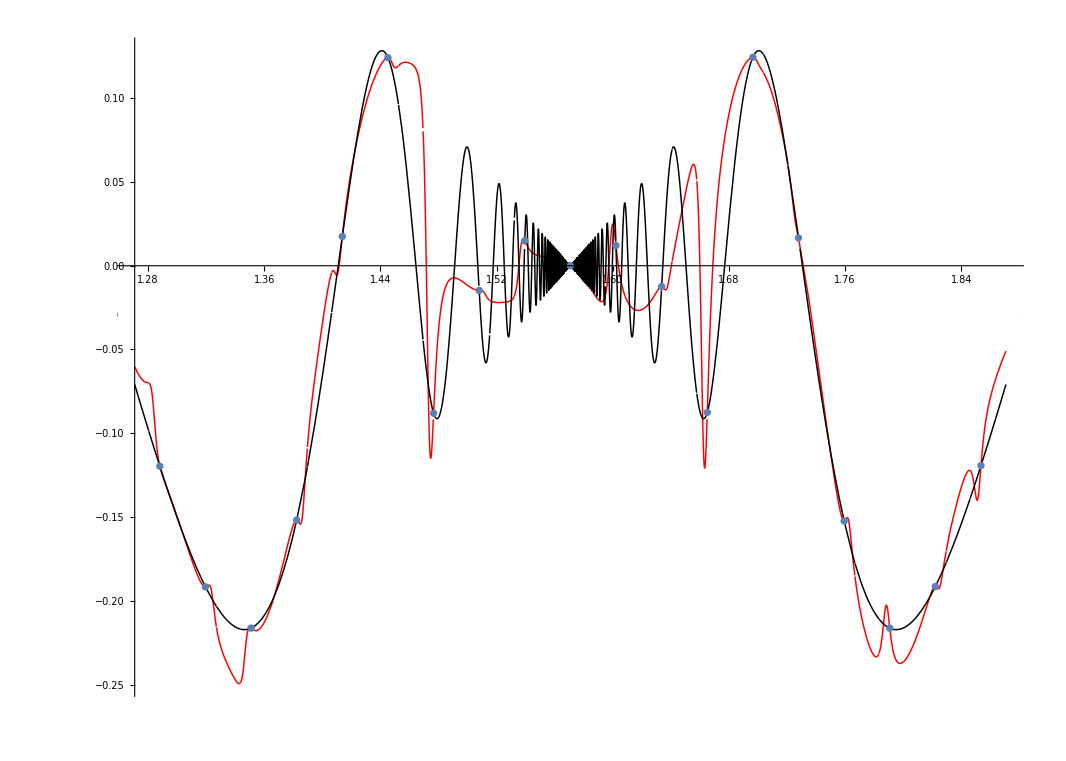

```mathematica
directorio=Directory[]

ftest[z_]=(z+1/z)/2 Sin[1/((z+1/z)/2)]


Attributes[ftest]={Listable}



(* random.wls obtains the system of arcs related with the random device and write it as arcosalpha *)

n=100;T=2*Pi;

Get["Dropbox/articulo2023/random.wls"]



(* arcos.wls obtains all the system of arcs related with arcosalpha in the sense of the paper and the related nodal systems *)
Get["Dropbox/atypeofinterpolation2023/arcos.wls"]

(* derivadas.wls obtains the derivatives used in the paper for a nodal system in T *)
listaalpha=alphaW2n;listaarcosalpha=arcosalphaW2n;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];
derivadasalphaW2n=derivadas;
derivadassegundasalphaW2n=derivadas*factoresderivadassegundas;

(* same comment as before *)
listaalpha=alphaYn;listaarcosalpha=arcosalphaYn;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];
derivadasalphaYn=derivadas;
derivadassegundasalphaYn=derivadas*factoresderivadassegundas;




(* same comment as before *)
listaalpha=alphaZn;listaarcosalpha=arcosalphaZn;
Get["Dropbox/atypeofinterpolation2023/derivadas.wls"];
derivadasalphaZn=derivadas;
derivadassegundasalphaZn=derivadas*factoresderivadassegundas;

(* u and v in the sense of the paper *)
u=ftest[alphaW2n];v=ftest'[alphaW2n];

(* semi Hermite and semi Hermite-Fejer interpolants usin the barycentric formulae*)

SHFejer[z_]=(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]]u[[2k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)u[[2k-1]]))/(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)));

SHerm[z_]=(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]]u[[2k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)u[[2k-1]])+∑_(k=1)^(n/5) (alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]])v[[2k-1]])+∑_(k=4n/5)^n (alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]])v[[2k-1]]))/(∑_(k=1)^n ((alphapwp[[2k]]derivadasalphaZn[[k]])/((z-alphaW2n[[2k]])(derivadasalphaW2n[[2k]])^2)+alphapwp[[2k-1]]/((z-alphaW2n[[2k-1]])derivadasalphaW2n[[2k-1]]derivadasalphaYn[[k]]) (1/(z-alphaW2n[[2k-1]])-derivadassegundasalphaW2n[[2k-1]]/(2 derivadasalphaW2n[[2k-1]])-derivadassegundasalphaYn[[k]]/(2 derivadasalphaYn[[k]])+(3n)/2)));





BB=Plot[{Re[SHerm[E^(I x)]],Re[ftest[E^(I x)]]},{x,0,Pi/2+.3}, PlotRange->Full,PlotPoints->100,PlotStyle->{{Red,Thickness[.001]},{Black,Thickness[.001]}},AspectRatio->5/7];
BB1=Plot[{Re[SHFejer[E^(I x)]],Re[ftest[E^(I x)]]},{x,Pi/2-0.3,Pi/2+.3}, PlotRange->Full,PlotPoints->200,PlotStyle->{{Red,Thickness[.001]},{Black,Thickness[.001]}},AspectRatio->5/7];




AA=Table[{Re[Log[alphaW2n[[k]]]/I],Re[ftest[alphaW2n[[k]]]]},{k,1,2n}];
AA=ListPlot[AA,PlotStyle->PointSize[.005]];
Show[BB,AA]
Show[BB1,AA]
```